```mathematica
Plot3D[
x^2,{x,-2,2},{y,-2,2},
BoxRatios->Automatic,
RegionFunction->
Function[{x,y,z},x^2+y^2<4],
BoundaryStyle->{Thick, Gray},
Filling->Bottom,
FillingStyle->{Green,Opacity[0.3]},
Mesh->8,
MeshShading->{{Black,White},{White,Black}},
PlotTheme->"Monochrome"
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Cos[x],{x,0,2π},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Cos[x],{x,0,2π},{θ,0,π},
Boxed->False,Axes->False
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2π},
Mesh->9,
MeshShading->{{GrayLevel[0.8], None}, {None,GrayLevel[0.8]}}
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{{x^2},{Cos[x]}},{x,0,2π},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x+y],{x,0,2π},{y,0,2π},PlotTheme->"Classic"]
```

-Graphics3D-

-Graphics3D-

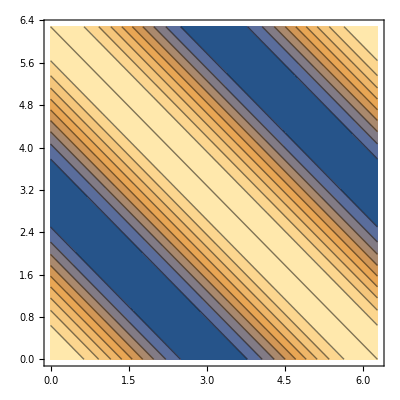

```mathematica
ContourPlot[Cos[x+y],{x,0,2 π},{y,0,2π}]
```

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

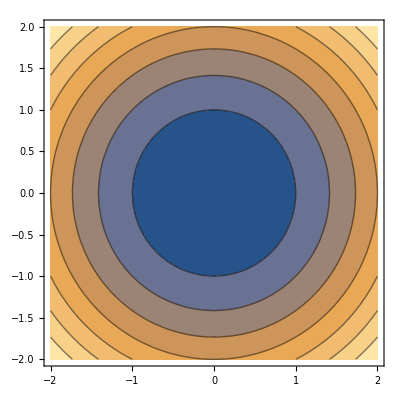

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2}]
```

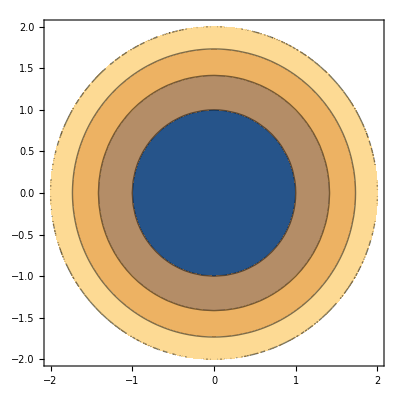

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y},x^2+y^2<4]
]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-2,2},{y,-2,2},{z,-2,2}

]
```

-Graphics3D-

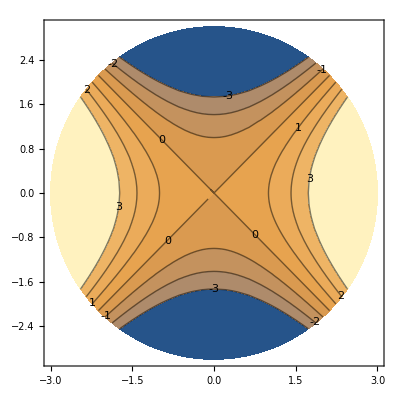

```mathematica
ContourPlot[x^2-y^2,{x,-3,3},{y,-3,3},
Contours->{-3,-2,-1,0,1,2,3},
RegionFunction->Function[{x,y},x^2+y^2<9],
ContourLabels->True
]
```

```mathematica
ContourPlot3D[x y z ,{x,-2,2},{y,-2,2},{z,-2,2},
Contours->{-2,-1,0,1,2},PlotTheme->"Detailed",
ContourStyle->{Opacity[0.8]},
Mesh->False
]
```

-Graphics3D-

```mathematica
ContourPlot3D[x y z ,{x,-2,2},{y,-2,2},{z,-2,2},
ContourStyle->{Opacity[0.8]},
Mesh->False
]
```

-Graphics3D-

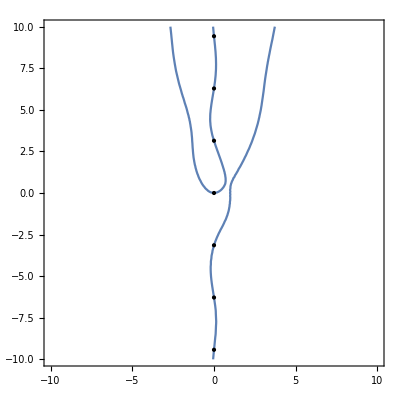

```mathematica
ContourPlot[
x y +x^2-Sin[y]-x^3==0,
{x,-10,10},{y,-10,10},
Epilog->Table[Point[{0,k π}],{k,-3,3}]
]
```

```mathematica
helix = ParametricPlot3D[
{Cos[t],Sin[t],t},{t,0,2π},
PlotStyle->{Thickness[0.02]}
]
```

-Graphics3D-

```mathematica
r =1;
R=1.5;
p=2;
q=3;
knot=ParametricPlot3D[
{R Cos[p t]+r Cos[p t]Cos[q t],R Sin[p t]+r Sin[p t]Cos[q t],r Sin[q t]},
{t,0,2π},
PlotRange->1.1{{-r-R,r+R},{-r-R,r+R},{-r,r}},
PlotStyle->{Tube[0.1]}
]
```

-Graphics3D-

-Graphics3D-

```mathematica
torus = RevolutionPlot3D[
{R+r Cos[t],r Sin[ t]},
{t,0,2π},
PlotRange->1.1{{-r-R,r+R},{-r-R,r+R},{-r,r}},
Mesh->None,
PlotStyle->{Opacity[0.95]},
PlotTheme->"Classic"
];
Show[torus,knot]
```

-Graphics3D-

```mathematica
cyl = Graphics3D[
{
{Opacity[0.2],
Cylinder[{{0,0,0},{0,0,2π}},1]},
{Red,Thickness[0.05],Cylinder[{{0,0,0},{0,0,2π}},0.1]}
}
]
```

-Graphics3D-

```mathematica
Show[helix,cyl,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Graphics3D[
{
{Red,Table[Sphere[{i,j,k},0.25],{i,-1,1,2},{j,-1,1,2},{k,-1,1,2}]},
{Red,Sphere[{0,0,0},0.25]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j,k+1}},0.1],{i,-1,1},{j,-1,1},{k,-1,0}]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j+1,k}},0.1],{i,-1,1},{j,-1,0},{k,-1,1}]},
{Cyan,Table[Cylinder[{{i,j,k},{i+1,j,k}},0.1],{i,-1,0},{j,-1,1},{k,-1,1}]}
}
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
{Red,Table[Sphere[{i,j,k},0.25],{i,-1,1,2},{j,-1,1,2},{k,-1,1,2}]},
{Red,Table[Sphere[{0,0,k},0.25],{k,-1,1,2}]},
{Red,Table[Sphere[{0,j,0},0.25],{j,-1,1,2}]},
{Red,Table[Sphere[{i,0,0},0.25],{i,-1,1,2}]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j,k+1}},0.1],{i,-1,1},{j,-1,1},{k,-1,0}]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j+1,k}},0.1],{i,-1,1},{j,-1,0},{k,-1,1}]},
{Cyan,Table[Cylinder[{{i,j,k},{i+1,j,k}},0.1],{i,-1,0},{j,-1,1},{k,-1,1}]}
}
,Axes->True
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
{Red,Table[Sphere[{i,j,k},0.25],{i,-1,1},{j,-1,1},{k,-1,1}]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j,k+1}},0.1],{i,-1,1},{j,-1,1},{k,-1,0}]},
{Cyan,Table[Cylinder[{{i,j,k},{i,j+1,k}},0.1],{i,-1,1},{j,-1,0},{k,-1,1}]},
{Cyan,Table[Cylinder[{{i,j,k},{i+1,j,k}},0.1],{i,-1,0},{j,-1,1},{k,-1,1}]}
}
]
```

-Graphics3D-

```mathematica
(* Draw Lissajous knots *)
nx=3;
ny=5;
nz=7;
ϕy=π/4;
ϕx=0;
ϕz=π/12;
Lissajous_knots = ParametricPlot3D[
{Cos[nx t +ϕx],Cos[ny t +ϕy],Cos[nz t +ϕz]},{t,0,2π},
PlotStyle->{Tube[0.02]}
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[
Sin[x],{x,-π/2,0},BoxRatios->{1,1,6}
]
```

-Graphics3D-

```mathematica
RegionPlot3D[z≥0 && z≤5(1-√(x^2+y^2)),{x,-1,1},{y,-1,1},{z,0,5}]
```

-Graphics3D-

```mathematica
Manipulate[
Graphics3D[
Table[
Line[{{a,b,c},{Cos[t],Sin[t],0}}],
{t,0.0,2π,(2π)/50.0}
],
PlotRange->{{-2,2},{-2,2},{0,5}}
],
{a,-2,2},{b,-2,2},{{c,5},0,5}
]
```